## Plotting of ψ(x,t)

We will assume the wavefunctions ψ_i are for a particle of unit mass in a 1D box of unit length. In natural units, we can take ℏ = 1.

```mathematica
ℏ = 1;m=1;L=1;
```

The energy values are:

```mathematica
E1=(Pi^2 ℏ^2)/(2m L^2);E2=4E1;E3=9E1;
```

Time independent wavefunctions:
ψ_n=√(2/L)Sin(n*Pi*x/L)

So, the given time-dependent wavefunction is:

```mathematica
ψ[x_,t_]:=1/(√6)Exp[-I E1 t/ℏ] √(2/L)Sin[Pi*x/L] +I/(√2)Exp[-I E2 t/ℏ] √(2/L)Sin[2Pi*x/L]+1/(√3)Exp[-I E3 t/ℏ] √(2/L)Sin[3Pi*x/L];
```

This will have both a real and an imaginary part, so we can plot both of them like this:

```mathematica
Manipulate[Plot3D[{Re[ψ[x,t]],Im[ψ[x,t]]},{x,0,1},{t,0,tmax},ImageSize->Large,AxesLabel->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14}],{tmax,0.1,2}]
```

We can plot the probability density of the wavefunction like this:

```mathematica
Plot3D[Abs[ψ[x,t]]^2,{x,0,1},{t,0,2},ImageSize->Large,AxesLabel->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

-Graphics3D-

We can also visualize it as a density plot:

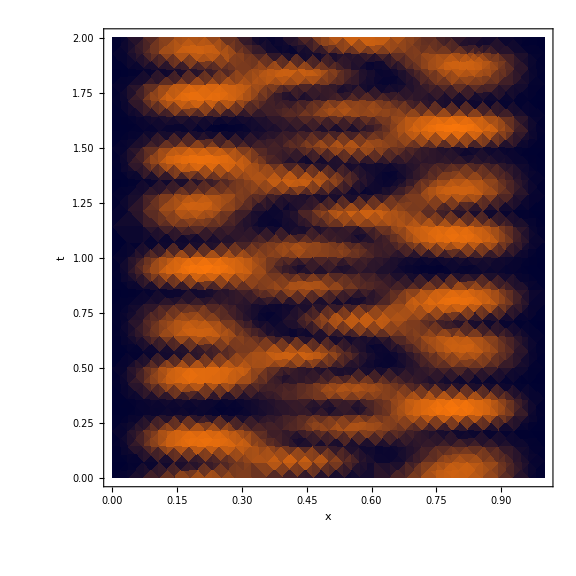

```mathematica
DensityPlot[Abs[ψ[x,t]]^2,{x,0,1},{t,0,2},ColorFunction->ColorData["RustTones"], ImageSize->Large,FrameLabel->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

The average energy for the system is given by
<E> = ∑_(i=1)^n Abs[C_i]^2 E_i

```mathematica
Eavg =Abs[1/(√6)]^2 E1 + Abs[I/(√2)]^2 E2 + Abs[1/(√3) ]^2 E3
```

(31 π^2)/12